# Actividad 3

## Wei Le Hu Tang

En respuesta a la glucosa, las células β de los islotes pancreáticos secretan insulina, lo que causa el uso o consumo de glucosa en tejidos como músculo, hígado y tejido adiposo. Cuando los niveles de glucosa en la sangre disminuyen, la secreción de insulina se detiene y los tejidos comienzan a utilizar sus reservas de energía. La interrupción de este sistema de control resulta en diabetes. Se cree que los impulsos eléctricos juegan un papel importante en la liberación de insulina por parte de las células. Un posible mecanismo para la generación de estos impulsos es a través del modelo de FitzHugh-Nagumo



donde  es la corriente aplicada a la célula y  y  son parámetros positivos.

## Si , y , las primeras dos ecuaciones se desacoplan de la tercera. Encuentra todos los puntos de equilibrio de las primeras dos ecuaciones.

Si se cumple que ,  y , el modelo queda:



Donde la última igualdad nos indica que  es constante, en particular 
Los puntos de equilibrio están dados por:




Determinemos las soluciones de esta ecuación

```mathematica
(*coordenada x en los puntos de equilibrio*)
solx0=x/.Solve[x^2(x+2)==1,x];
solx0
```

{-1,1/2 (-1-√5),1/2 (-1+√5)}

Usando , se puede llegar a que , tal que sustityendo en las  anteriores se obtiene que:

```mathematica
(*coordenada y en los puntos de equilibrio por regla de correspondencia*)
soly0={};
For[i=1,i<=3,i++,AppendTo[soly0,1-5solx0[[i]]^2]]
soly0
```

{-4,1-5/4 (-1-√5)^2,1-5/4 (-1+√5)^2}

Por lo tanto los puntos de equilibrio dado ,  y  son

```mathematica
(*lista de puntos de equilibrio*)
pde0={};
For[i=1,i<=3,i++,AppendTo[pde0,{solx[[i]],soly[[i]]}]];
pde0
```

{{-1,-4},{1/2 (-1-√5),1-5/4 (-1-√5)^2},{1/2 (-1+√5),1-5/4 (-1+√5)^2}}

## Determina la estabilidad de los puntos de equilibrio del punto anterior y bosqueja el retrato fase de las soluciones.

La matriz Jacobiana asociada a este problema es
 (nota: sé que se ve muy feo con los ‘(‘, pero si no se los ponía se veía peor)

Por el curso de ecuaciones diferenciales, se sabe que, dado un punto de equilibrio , si el determinante  es un punto silla; por otro lado, si  y la traza , entonces es inestable, y de lo contrario , entonces es estable.
Evalúese entonces el Jacobiano en los puntos de equilibrio encontrados:


 es un punto silla

Para los otros dos casos crearemos funciones de apoyo

```mathematica
(*define la matriz jacobiana que, en este caso, sólo depende de x*)
J[x_]={{-3x^2+6x,1},{-10x,-1}};
(*regresa los signos del determinante y la traza respectivamente*)
DetTrSign[mat_]={Positive[Det[mat]],Positive[Tr[mat]]};

(*matriz jacobiana del segundo punto*)
jac2=J[-(1+Sqrt[5])/2];
MatrixForm[jac2]
(*Estabilidad del segundo punto*)
DetTrSign[jac2]
```

(3 (-1-√5)-3/4 (-1-√5)^2 | 1
-5 (-1-√5) | -1)

{True,False}

es estable

```mathematica
(*matriz jacobiana del tercer punto*)
jac3=J[(-1+Sqrt[5])/2];
MatrixForm[jac3]
(*Estabilidad del tercer punto*)
DetTrSign[jac3]
```

(3 (-1+√5)-3/4 (-1+√5)^2 | 1
-5 (-1+√5) | -1)

{True,True}

es inestable

Retrato fase, ceroclinas, y puntos de equilibrio:

Las ceroclinas para este sistema son:

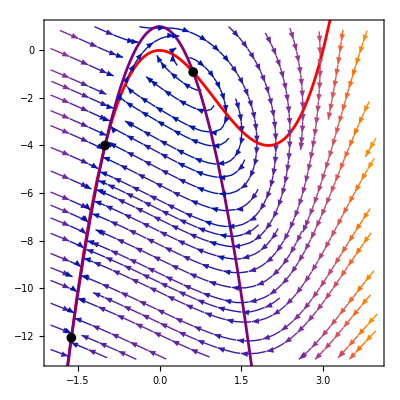

```mathematica
(*ecuaciones diferenciales*)
dx[x_,y_]=y-x^3+3x^2;
dy[x_,y_]=1-5x^2-y;

(*retrato fase, ceroclinas, puntos de equilibrio respectivamente*)
Show[StreamPlot[{dx[x,y],dy[x,y]},{x,-2,4},{y,-13,1}],
	Plot[{x^3-3x^2,1-5x^2},{x,-2,4},PlotStyle->{Red,Purple}],
	ListPlot[pde,PlotStyle->{Black},PlotMarkers->{Automatic,Medium}]]
```

## Repite lo anterior con , e . Explica cómo son los cambios en el retrato fase conforme cambia.

Resolviendo 







Por otro lado, las ceroclinas son:


 sólo hace que varíe , entonces a continuación sólo se redefinirá ésta ecuación, y se usará la misma 

Más aun,  al ser una constante, no afecta en las derivadas parciales del sistema, por lo que la matriz Jacobiana es igual a la del inciso anterior

#### Soluciones de equilibrio

```mathematica
(*coordenada x de las soluciones*)
solx04=x/.Solve[x^2(x+2)==0.4+1,x]
```

{-1.35886-0.322617 ⅈ,-1.35886+0.322617 ⅈ,0.71773}

Sólo la tercera solución es real, entonces es la que se tomará en cuenta, la coordenada  se puede obtener con la ecuación de su ceroclina

```mathematica
(*coordenada y de la solución*)
soly04=1-5solx04[[3]]^2
```

-1.57568

```mathematica
(*punto de equilibrio*)
```

```mathematica
pde04={{solx04[[3]],soly04}}
```

{{0.71773,-1.57568}}

#### Estabilidad

```mathematica
(*matriz jacobiana del punto de equilibrio*)
jac04=J[solx04[[3]]];
MatrixForm[jac04]
(*Estabilidad del segundo punto*)
DetTrSign[jac04]
```

(2.76097 | 1
-7.1773 | -1)

{True,True}

es inestable

#### Retrato fase, ceroclinas y puntos de equilibrio

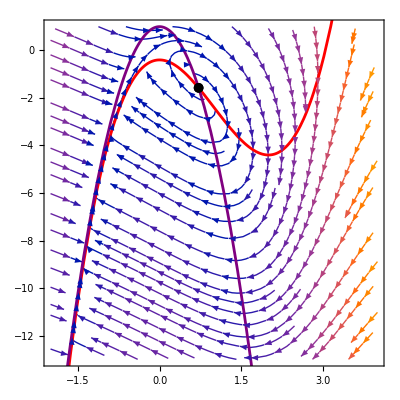

```mathematica
(*ecuación diferencial de x, con I=0.4*)
dx04[x_,y_]=y-x^3+3x^2+0.4;

(*retrato fase, ceroclinas, puntos de equilibrio respectivamente*)
Show[StreamPlot[{dx04[x,y],dy[x,y]},{x,-2,4},{y,-13,1}],
	Plot[{x^3-3x^2-0.4,1-5x^2},{x,-2,4},PlotStyle->{Red,Purple}],
	ListPlot[pde04,PlotStyle->{Black},PlotMarkers->{Automatic,Medium}]]
```

#### Soluciones de equilibrio

```mathematica
(*coordenada x de las soluciones*)
solx2=x/.Solve[x^2(x+2)==2+1,x]
```

{1,1/2 (-3-ⅈ √3),1/2 (-3+ⅈ √3)}

Sólo la primera solución es real, entonces es la que se tomará en cuenta

```mathematica
(*coordenada y de la solución*)
soly2=1-5solx2[[1]]^2
```

-4

```mathematica
(*punto de equilibrio*)
```

```mathematica
pde2={{solx2[[1]],soly2}}
```

{{1,-4}}

#### Estabilidad

```mathematica
(*matriz jacobiana del punto de equilibrio*)
jac2=J[1];
MatrixForm[jac2]
(*Estabilidad del segundo punto*)
DetTrSign[jac2]
```

(3 | 1
-10 | -1)

{True,True}

es inestable

#### Retrato fase, ceroclinas y puntos de equilibrio

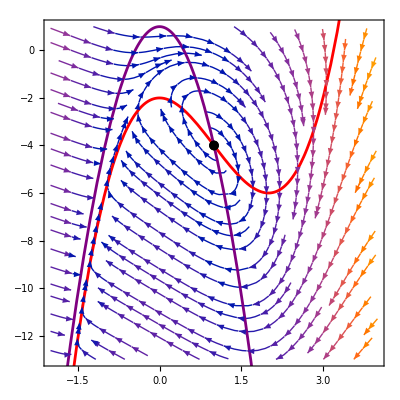

```mathematica
(*ecuación diferencial de x, con I=2*)
dx2[x_,y_]=y-x^3+3x^2+2;

(*retrato fase, ceroclinas, puntos de equilibrio respectivamente*)
Show[StreamPlot[{dx2[x,y],dy[x,y]},{x,-2,4},{y,-13,1}],
	Plot[{x^3-3x^2-2,1-5x^2},{x,-2,4},PlotStyle->{Red,Purple}],
	ListPlot[pde2,PlotStyle->{Black},PlotMarkers->{Automatic,Medium}]]
```

#### Soluciones de equilibrio

```mathematica
(*coordenada x de las soluciones*)
solx4=x/.Solve[x^2(x+2)==4+1,x]
```

{Root1.24Root[-5+2 #1^2+#1^3&,1]1.2418965630344798,Root-1.62-1.18 ⅈRoot[-5+2 #1^2+#1^3&,2]-1.6209482815172398,Root-1.62+1.18 ⅈRoot[-5+2 #1^2+#1^3&,3]-1.6209482815172398}

Sólo la primera solución es real, entonces es la que se tomará en cuenta

```mathematica
(*coordenada y de la solución*)
soly4=1-5solx4[[1]]^2
```

1-5 (Root1.24Root[-5+2 #1^2+#1^3&,1]1.2418965630344798)^2

```mathematica
(*punto de equilibrio*)
```

```mathematica
pde4={{solx4[[1]],soly4}}
```

{{Root1.24Root[-5+2 #1^2+#1^3&,1]1.2418965630344798,1-5 (Root1.24Root[-5+2 #1^2+#1^3&,1]1.2418965630344798)^2}}

#### Estabilidad

```mathematica
(*matriz jacobiana del punto de equilibrio*)
jac4=J[solx4[[1]]];
MatrixForm[jac4]
(*Estabilidad del segundo punto*)
DetTrSign[jac4]
```

(6 Root1.24Root[-5+2 #1^2+#1^3&,1]1.2418965630344798-3 (Root1.24Root[-5+2 #1^2+#1^3&,1]1.2418965630344798)^2 | 1
-10 Root1.24Root[-5+2 #1^2+#1^3&,1]1.2418965630344798 | -1)

{True,True}

es inestable

#### Retrato fase, ceroclinas y.08 puntos de equilibrio

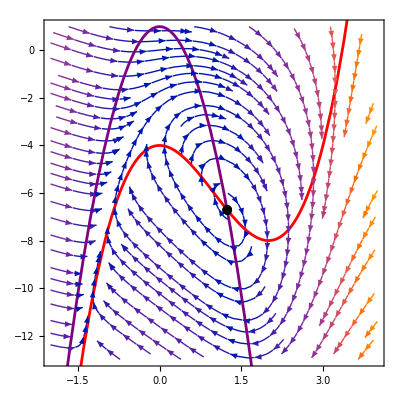

```mathematica
(*ecuación diferencial de x, con I=0.4*)
dx4[x_,y_]=y-x^3+3x^2+4;

(*retrato fase, ceroclinas, puntos de equilibrio respectivamente*)
Show[StreamPlot[{dx4[x,y],dy[x,y]},{x,-2,4},{y,-13,1}],
	Plot[{x^3-3x^2-4,1-5x^2},{x,-2,4},PlotStyle->{Red,Purple}],
	ListPlot[pde4,PlotStyle->{Black},PlotMarkers->{Automatic,Medium}]]
```

```mathematica
Manipulate[Show[StreamPlot[{y-x^3+3x^2+I,dy[x,y]},{x,-2,4},{y,-13,1}],
	Plot[{x^3-3x^2-I,1-5x^2},{x,-2,4},PlotStyle->{Red,Purple}],
	ParametricPlot[{
	Evaluate[{x[t],y[t]}/.NDSolve[
{x'[t]==y[t]-x[t]^3+3x[t]^2+I,
y'[t]==1-5x[t]^2-y[t],
x[0]==-2,y[0]==0},
{x,y},{t,0,50}]],
	Evaluate[{x[t],y[t]}/.NDSolve[
{x'[t]==y[t]-x[t]^3+3x[t]^2+I,
y'[t]==1-5x[t]^2-y[t],
x[0]==1,y[0]==-6},
{x,y},{t,0,50}]]},
{t,0,50},PlotStyle->{Green,Yellow}]],
{I,0,10}]
```

es un impulso eléctrico, por lo que . La única ecuación que se ve afectada por este parámetro es , y su ceroclina , entonces si crecce , la ceroclina de  se desplaza “hacia abajo”, al ser ésta de mayor orden que la ceroclina de , llega un momento en que dejan de intersectarse tres veces (existir tres soluciones), porque el tramo de la gráfcia que puede volver a intersectar queda dentro de la región convexa de la ceroclina de , dejando una única solución de equilibrio inestable de tipo espiral. Más aun, como se puede ver en las trayectorias verde y amarillo, el sistema tienda a un ciclo límite.

## Para , e , resuelve el sistema de ecuaciones y grafica las series de tiempo de , y en una sola gráfica.

```mathematica
M=10;
Manipulate[Show[Plot[Evaluate[
{x[t],y[t],z[t]}/.NDSolve[
{x'[t]==y[t]-x[t]^3+3x[t]^2+0.4-z[t],
y'[t]==1-5x[t]^2-y[t],
z'[t]==r(s(x[t]+(1+Sqrt[5])/2)-z[t]),
x[0]==x0,y[0]==y0,z[0]==z0
},{x,y,z},{t,0,5M}]
],{t,0,5M}]],{x0,-M,M},{y0,-M,M},{z0,-M,M},{r,0,M},{s,0,M}]
```

```mathematica
M=10;
Manipulate[Show[Plot[Evaluate[
{x[t],y[t],z[t]}/.NDSolve[
{x'[t]==y[t]-x[t]^3+3x[t]^2+2-z[t],
y'[t]==1-5x[t]^2-y[t],
z'[t]==r(s(x[t]+(1+Sqrt[5])/2)-z[t]),
x[0]==x0,y[0]==y0,z[0]==z0
},{x,y,z},{t,0,10M}]
],{t,0,5M}]],{x0,-M,M},{y0,-M,M},{z0,-M,M},{r,0,M},{s,0,M}]
```

```mathematica
M=10;
Manipulate[Show[Plot[Evaluate[
{x[t],y[t],z[t]}/.NDSolve[
{x'[t]==y[t]-x[t]^3+3x[t]^2+4-z[t],
y'[t]==1-5x[t]^2-y[t],
z'[t]==r(s(x[t]+(1+Sqrt[5])/2)-z[t]),
x[0]==x0,y[0]==y0,z[0]==z0
},{x,y,z},{t,0,5M}]
],{t,0,5M}]],{x0,-M,M},{y0,-M,M},{z0,-M,M},{r,0,M},{s,0,M}]
```

Para valores pequeños de  como el caso de , la convergencia del modelo (a constantes o a ciclos) es más sensible a las condiciones iniciales, mientras que para valores más grandes como  , depende únicamente de los parámetros  y .

## Para los valores de del punto anterior, encuentra los puntos de equilibrio del sistema y bosqueja los retratos fase de: contra , contra y contra .

```mathematica
dx[x_,y_,z_,c_]=y-x^3+3x^2+c-z;
dy[x_,y_]=1-5x^2-y;
dz[x_,z_,r_,s_]=r(s(x+(1+Sqrt[5])/2)-z);
```

### Soluciones generales del sistema

(1)
				(2)
		(3)

Por (1) y (2)

				(4)
		(5)

Por (3)

		(6)

Regresando a (5)

Por lo tanto, dados los parámetros , la coordenada  de las soluciones está dado por las raíces de este polinomio, donde todo lo de la derecha en la expresión de abajo es una constante.


Dadas las soluciones en , las otras dos coordenadas se pueden obtener mediante (4) y (6)

```mathematica
M=10;
Manipulate[
{Manipulate[StreamPlot[{dx[x,y,z,0.4],dy[x,y]},{x,-2,4},{y,-13,1}],
{z,-M,M}],
Manipulate[StreamPlot[{dx[x,y,z,0.4],dz[x,z,r,s]},{x,-4,4},{z,-10,10}],
{y,-M,M}],
Manipulate[StreamPlot[{dy[x,y],dz[x,z,r,s]},{y,-10,10},{z,-10,10}],
{x,-M,M}]
},{r,0,M},{s,0,M}]
```

```mathematica
M=10;
Manipulate[
{Manipulate[StreamPlot[{dx[x,y,z,2],dy[x,y]},{x,-2,4},{y,-13,1}],
{z,-M,M}],
Manipulate[StreamPlot[{dx[x,y,z,2],dz[x,z,r,s]},{x,-4,4},{z,-10,10}],
{y,-M,M}],
Manipulate[StreamPlot[{dy[x,y],dz[x,z,r,s]},{y,-10,10},{z,-10,10}],
{x,-M,M}]
},{r,0,M},{s,0,M}]
```

```mathematica
M=10;
Manipulate[
{Manipulate[StreamPlot[{dx[x,y,z,4],dy[x,y]},{x,-2,4},{y,-13,1}],
{z,-M,M}],
Manipulate[StreamPlot[{dx[x,y,z,4],dz[x,z,r,s]},{x,-4,4},{z,-10,10}],
{y,-M,M}],
Manipulate[StreamPlot[{dy[x,y],dz[x,z,r,s]},{y,-10,10},{z,-10,10}],
{x,-M,M}]
},{r,0,M},{s,0,M}]
```